```mathematica
datadistruibution=Import["C:\\Users\\muxy1\\OneDrive\\桌面\\E1.xlsx"];
```

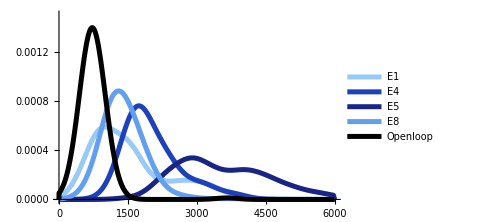

```mathematica
SmoothHistogram[{datadistruibution[[1]][[1]],datadistruibution[[1]][[2]],datadistruibution[[1]][[3]],datadistruibution[[1]][[4]],datadistruibution[[1]][[5]]},250,PlotRange->{{0,6000},{0,0.0015}},PlotLegends->{"E1","E4","E5","E8","Openloop"},PlotStyle->{Directive[RGBColor["#97caf7"],Thickness[0.01]],Directive[RGBColor["#1e40bd"],Thickness[0.01]],Directive[RGBColor["#192586"],Thickness[0.01]],Directive[RGBColor["#639fef"],Thickness[0.01]],Directive[Black,Thickness[0.01]]},AxesStyle->Directive[Black, 12],ImageSize->Medium]
```

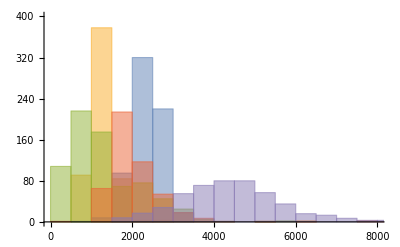

```mathematica
Histogram[{datadistruibution[[1]][[1]],datadistruibution[[1]][[2]],datadistruibution[[1]][[3]],datadistruibution[[1]][[4]],datadistruibution[[1]][[5]]},PlotRange->{{0,8000},{0,400}}]
```

```mathematica
datadistruibution2=Import["C:\\Users\\muxy1\\OneDrive\\桌面\\E1 - Copy.xlsx"];
```

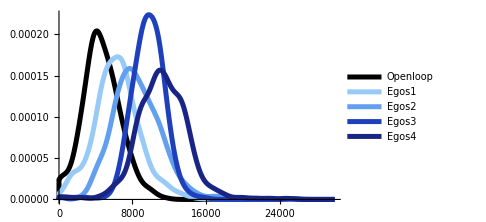

```mathematica
SmoothHistogram[{datadistruibution2[[1]][[1]],datadistruibution2[[1]][[2]],datadistruibution2[[1]][[3]],datadistruibution2[[1]][[4]],datadistruibution2[[1]][[5]]},650,PlotRange->{{0,30000},Automatic},PlotLegends->{"Openloop","Egos1","Egos2","Egos3","Egos4"},PlotStyle->{Directive[Black,Thickness[0.01]],Directive[RGBColor["#97caf7"],Thickness[0.01]],Directive[RGBColor["#639fef"],Thickness[0.01]],Directive[RGBColor["#1e40bd"],Thickness[0.01]],Directive[RGBColor["#192586"],Thickness[0.01]]},AxesStyle->Directive[Black, 12],ImageSize->Medium]
```

```mathematica
z
```

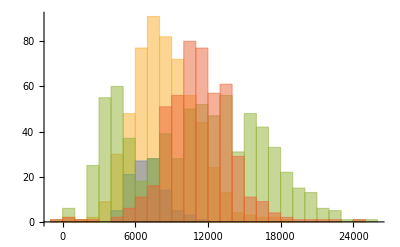

```mathematica
Histogram[{datadistruibution2[[1]][[1]],datadistruibution2[[1]][[2]],datadistruibution2[[1]][[3]],datadistruibution2[[1]][[4]]}]
```